# Graph Decomposition

```mathematica
Clear["Global`*"]
```

Let H be a graph with n edges. If there exists ρ-labeling for graph H then H decomposes a complete graph K_{2n+1}
Ex:  Let H be a triangle a let {0, 2, 3} be a vertex labeling of H. Then, this is a ρ-labeling and thus H decomposes K_7

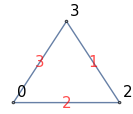

```mathematica
v={0,2,3};
edges={v[[1]]<->v[[2]],v[[2]]<->v[[3]],v[[3]]<->v[[1]]};
edgeNames=Table[EdgeList[edges][[k]][[1]]<->EdgeList[edges][[k]][[2]]->Abs[EdgeList[edges][[k]][[2]]-EdgeList[edges][[k]][[1]]],{k,1,Length[EdgeList[edges]]}]; 
Graph[edges,VertexLabels->"Name", EdgeLabels->edgeNames,GraphLayout->Automatic,EdgeLabelStyle->Directive[Red,15], VertexLabelStyle->Directive[Black,15]]
```

```mathematica
Manipulate[
n=7; (* n = |E(H)|, H with ρ-labeling decomposes K_{2n+1} *)
K=CompleteGraph[n,VertexLabels->"Name"];
If[click>=1,
For[i=1,i≤click,i++,
v=Mod[{0,2,3}+i,n];
v=v+1;
K=HighlightGraph[K,{v[[1]]<->v[[2]],v[[2]]<->v[[3]],v[[3]]<->v[[1]]}]];
v=v-1,
K=CompleteGraph[n,VertexLabels->"Name"];
];
Graph[K],
{click,0,7,1, Appearance->"Labeled"},TrackedSymbols:>{click}
]
```

Another Example:
Let H be a graph defined by:

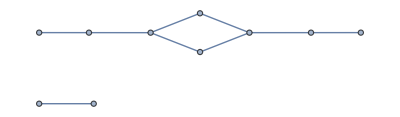

```mathematica
v={15,7,0,4,6,1,3,2,9,18};
edges={v[[1]]<->v[[2]],v[[2]]<->v[[3]],v[[3]]<->v[[4]],v[[3]]<->v[[5]],v[[5]]<->v[[6]],v[[4]]<->v[[6]],v[[6]]<->v[[7]],v[[7]]<->v[[8]],v[[9]]<->v[[10]]};
Graph[edges]
```

In fact, v is a ρ-labeling:

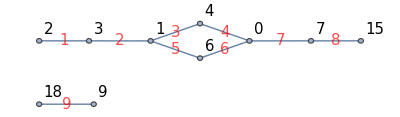

```mathematica
edgeNames=Table[EdgeList[edges][[k]][[1]]<->EdgeList[edges][[k]][[2]]->Abs[EdgeList[edges][[k]][[2]]-EdgeList[edges][[k]][[1]]],{k,1,Length[EdgeList[edges]]}]; 
Graph[edges,VertexLabels->"Name", EdgeLabels->edgeNames,GraphLayout->Automatic,EdgeLabelStyle->Directive[Red,15], VertexLabelStyle->Directive[Black,15]]
```

Since H has 9 edges and v is a ρ-labeling, the graph H decomposes K_19:

```mathematica
n=Length[EdgeList[edges]]; (* n = |E(G)|, H with ρ-labeling decomposes K_{2n+1} *)
Manipulate[
K=CompleteGraph[2*n,VertexLabels->"Name"];
If[click>=1,
For[i=0,i≤click,i++,
v={15,7,0,4,6,1,3,2,9,18}; (* vertex rho-labeling *)
v=Mod[v+i,2*n];  (* clicking *)
v=v+1; (* Mathematica counts from 1, so wee need to get rid of zeros *)
edges={v[[1]]<->v[[2]],v[[2]]<->v[[3]],v[[3]]<->v[[4]],v[[3]]<->v[[5]],v[[5]]<->v[[6]],v[[4]]<->v[[6]],v[[6]]<->v[[7]],v[[7]]<->v[[8]],v[[9]]<->v[[10]]}; (* definition of the graph *)
K=HighlightGraph[K,edges];
v=v-1;
],
K=CompleteGraph[2*n,VertexLabels->"Name"];
];
Graph[K],
{click,0,2*n,1, Appearance->"Labeled"},TrackedSymbols:>{click}
]
```